```mathematica
appl=FinancialData["NASDAQ:AAPL","Close",All]
```

TimeSeries[…]

```mathematica
Transpose[{
appl["Dates"][[;;-2]],
Ratios@appl["Values"]
}]
```

{{Fri 12 Dec 1980 00:00:00GMT-8.,0.947826},{Mon 15 Dec 1980 00:00:00GMT-8.,0.926607},9854,{Mon 6 Jan 2020 00:00:00GMT-8.,0.995297},{Tue 7 Jan 2020 00:00:00GMT-8.,1.01609}}
 |  |  |  |

```mathematica
Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}]
```

{{Fri 12 Dec 1980 00:00:00GMT-8.,-0.0521738},{Mon 15 Dec 1980 00:00:00GMT-8.,-0.0733929},{Tue 16 Dec 1980 00:00:00GMT-8.,0.0247439},9853,{Mon 6 Jan 2020 00:00:00GMT-8.,-0.00470305},{Tue 7 Jan 2020 00:00:00GMT-8.,0.0160863}}
 |  |  |  |

```mathematica
Histogram[
Map[Last,Out[3]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
DateListPlot[
Out[3],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
data=Map[Last,Out[3]];
```

```mathematica
Histogram[
Map[Last,Out[3]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,PlotRange->Full
]
```

-Graphics-

```mathematica
FunctionCompile[Function[Typed[arg,"MachineInteger"],arg+1]]
```

CompiledCodeFunction[…]

```mathematica
FunctionCompile[Function[Typed[arg,"MachineInteger"],{arg}]]
```

CompiledCodeFunction[…]

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Value"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Value"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
select
]
]
]
```

TemporalData::invprp: The argument Value is not a valid property. Specify "Properties" to obtain a list of valid properties.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+TemporalData[TimeSeries,{«1»},True,12.][Value]].

Transpose::nmtx: The first two levels of {{DateObject[{1980,12,12,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,16,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1981,2,23,0,0,0.},Instant,Gregorian,-8.],DateObject[{1981,2,24,0,0,0.},Instant,Gregorian,-8.],«9808»},Ratios[-1+«12»[«1»][Value]]} cannot be transposed.

TemporalData::invprp: The argument Value is not a valid property. Specify "Properties" to obtain a list of valid properties.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Transpose::nmtx: The first two levels of {{DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1997,7,24,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,7,25,0,0,0.},Instant,Gregorian,-8.],«5650»},Ratios[-1+«1»[Value]]} cannot be transposed.

Transpose::tperm: Permutation {{DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1997,7,24,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,7,25,0,0,0.},Instant,Gregorian,-8.],«5650»},Ratios[-1+«1»[Value]]} is longer than the dimensions {2} of the expression.

GatherBy::list: List expected at position 1 in «1».

GatherBy::list: List expected at position 1 in GatherBy[Transpose[{{DateObject[{1980,12,12,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,16,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1981,2,23,0,0,0.},Instant,Gregorian,-8.],DateObject[{1981,2,24,0,0,0.},Instant,Gregorian,-8.],«9808»},«1»},«1»]].

GatherBy[Transpose[{{Fri 12 Dec 1980 00:00:00GMT-8.,Mon 15 Dec 1980 00:00:00GMT-8.,Tue 16 Dec 1980 00:00:00GMT-8.,Wed 17 Dec 1980 00:00:00GMT-8.,9851,Fri 3 Jan 2020 00:00:00GMT-8.,Mon 6 Jan 2020 00:00:00GMT-8.,Tue 7 Jan 2020 00:00:00GMT-8.},Ratios[1]},{1}]]
 |  |  |  |

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Value"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Value"]]
}]
},
{trap,tram}
]
]
```

TemporalData::invprp: The argument Value is not a valid property. Specify "Properties" to obtain a list of valid properties.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[-1+TemporalData[TimeSeries,{«1»},True,12.][Value]].

Transpose::nmtx: The first two levels of {{DateObject[{1980,12,12,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,16,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1981,2,23,0,0,0.},Instant,Gregorian,-8.],DateObject[{1981,2,24,0,0,0.},Instant,Gregorian,-8.],«9808»},Ratios[-1+«12»[«1»][Value]]} cannot be transposed.

TemporalData::invprp: The argument Value is not a valid property. Specify "Properties" to obtain a list of valid properties.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Ratios::listrp: List or SparseArray or StructuredArray expected at position 1 in Ratios[«1»].

Transpose::nmtx: The first two levels of {{DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1997,7,24,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,7,25,0,0,0.},Instant,Gregorian,-8.],«5650»},Ratios[-1+«1»[Value]]} cannot be transposed.

$Aborted[]

```mathematica
ClearAll[appl,amzn]
```

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Value"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Value"]]
}]
},
{trap,tram}
]
]
```

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
Join[
Transpose[{
appl["Dates"][[;;-2]],
Table[r-1,{r,Ratios@appl["Value"]}]
}],
Transpose[{
amzn["Dates"][[;;-2]],
Table[r-1,{r,Ratios@amzn["Value"]}]
}]
]
]
```

TemporalData::invprp: The argument Value is not a valid property. Specify "Properties" to obtain a list of valid properties.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Table::iterb: Iterator {r,Ratios[TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{9859},StructuredArray`StructuredData[QuantityArray,{0.5134,0.486614,0.4509,0.462057,0.475457,«9850»,297.43,299.8,298.39,303.19},«1»,{«1»}]]},«6»},True,12.][…]]} does not have appropriate bounds.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

$Aborted[]

Transpose::nmtx: The first two levels of {{DateObject[{1980,12,12,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,16,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1981,2,23,0,0,0.},Instant,Gregorian,-8.],DateObject[{1981,2,24,0,0,0.},Instant,Gregorian,-8.],«9808»},Table[r-1,«1»]} cannot be transposed.

TemporalData::invprp: The argument Value is not a valid property. Specify "Properties" to obtain a list of valid properties.

Table::iterb: Iterator {r,Ratios[«1»]} does not have appropriate bounds.

Transpose::nmtx: The first two levels of {{DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1997,7,24,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,7,25,0,0,0.},Instant,Gregorian,-8.],«5650»},Table[r-1,{r,Ratios[«1»]}]} cannot be transposed.

Transpose::tperm: Permutation {{DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1997,7,24,0,0,0.},Instant,Gregorian,-8.],DateObject[{1997,7,25,0,0,0.},Instant,Gregorian,-8.],«5650»},Table[r-1,{r,Ratios[«1»]}]} is longer than the dimensions {2} of the expression.

Transpose[{{Fri 12 Dec 1980 00:00:00GMT-8.,Mon 15 Dec 1980 00:00:00GMT-8.,Tue 16 Dec 1980 00:00:00GMT-8.,Wed 17 Dec 1980 00:00:00GMT-8.,9850,Thu 2 Jan 2020 00:00:00GMT-8.,Fri 3 Jan 2020 00:00:00GMT-8.,Mon 6 Jan 2020 00:00:00GMT-8.,Tue 7 Jan 2020 00:00:00GMT-8.},1},1]
 |  |  |  |

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All]
},
Transpose[{
appl["Dates"][[;;-2]],
Table[r-1,{r,Ratios@appl["Value"]}]
}]
]
```

TemporalData::invprp: The argument Value is not a valid property. Specify "Properties" to obtain a list of valid properties.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Table::iterb: Iterator {r,Ratios[TemporalData[TimeSeries,{{StructuredArray[QuantityArray,{9859},StructuredArray`StructuredData[QuantityArray,{0.5134,0.486614,0.4509,0.462057,0.475457,«9850»,297.43,299.8,298.39,303.19},«1»,{«1»}]]},«6»},True,12.][…]]} does not have appropriate bounds.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{DateObject[{1980,12,12,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,15,0,0,0.},Instant,Gregorian,-8.],DateObject[{1980,12,16,0,0,0.},Instant,Gregorian,-8.],«45»,DateObject[{1981,2,23,0,0,0.},Instant,Gregorian,-8.],DateObject[{1981,2,24,0,0,0.},Instant,Gregorian,-8.],«9808»},Table[r-1,«1»]} cannot be transposed.

$Aborted[]

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
select
]
]
]
```

{{{Thu 15 May 1997 00:00:00GMT-8.,-0.0281672},{Thu 15 May 1997 00:00:00GMT-8.,-0.117407}},5698,{{Tue 7 Jan 2020 00:00:00GMT-8.,0.0160863},{Tue 7 Jan 2020 00:00:00GMT-8.,-0.00780866}}}
 |  |  |  |

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{

},
group
]
]
]
]
]
```

{{Thu 15 May 1997 00:00:00GMT-8.,{-0.0281672,-0.117407}},{Fri 16 May 1997 00:00:00GMT-8.,{-0.014607,-0.0115674}},5697,{Tue 7 Jan 2020 00:00:00GMT-8.,{0.0160863,-0.00780866}}}
 |  |  |  |

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Table[{First@First@p,Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]]},{p,part}]
]
]
]
]
]
```

{{Thu 15 May 1997 00:00:00GMT-8.,0.725681},{Fri 16 May 1997 00:00:00GMT-8.,0.658934},{Mon 19 May 1997 00:00:00GMT-8.,0.671851},5686,{Fri 20 Dec 2019 00:00:00GMT-8.,0.755902},{Mon 23 Dec 2019 00:00:00GMT-8.,0.671424}}
 |  |  |  |

```mathematica
DateListPlot[
Out[23],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[23]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
DateListPlot[
Out[23],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,Joined->False,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[23]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NASDAQ:AAPL","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NASDAQ:MSFT","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NASDAQ:FB","Close",All],
amzn=FinancialData["NASDAQ:AMZN","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NASDAQ:MSFT","Close",All],
amzn=FinancialData["NYSE:IBM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NYSE:CHK","Close",All],
amzn=FinancialData["NYSE:IBM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NASDAQ:AMZN","Close",All],
amzn=FinancialData["NYSE:IBM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NYSE:GE","Close",All],
amzn=FinancialData["NYSE:IBM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

-Graphics-

```mathematica
With[{
appl=FinancialData["NYSE:BAC","Close",All],
amzn=FinancialData["NYSE:IBM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

-Graphics-

```mathematica
With[{
appl=FinancialData["NYSE:BAC","Close",All],
amzn=FinancialData["NYSE:JPM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
Histogram[
Table[Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]],{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
]
]
]
]
]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

-Graphics-

```mathematica
With[{
appl=FinancialData["NYSE:BAC","Close",All],
amzn=FinancialData["NYSE:JPM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
DateListPlot[
Table[
{First@First@p,Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]]}
,{p,part}],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
]
]
]
]
]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

-Graphics-

```mathematica
With[{
appl=FinancialData["NYSE:BAC","Close",All],
amzn=FinancialData["NYSE:JPM","Close",All]
},
With[{
trap=Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
tram=Transpose[{
amzn["Dates"][[;;-2]],
Map[#-1&,Ratios@amzn["Values"]]
}]
},
With[{
select=Select[GatherBy[Join[trap,tram],First],Length@#==2&]
},
With[{
group=Table[{First@First@p,{Last@First@p,Last@Last@p}},{p,select}]
},
With[{
part=Partition[group,10,1]
},
DateListPlot[
Table[
{First@First@p,Correlation[Map[First@Last@#&,p],Map[Last@Last@#&,p]]}
,{p,part}][[;;-100]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow",Joined->False
]
]
]
]
]
]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

-Graphics-

```mathematica
Style[TableForm[WolframAlpha["treasury yield curve",{{"TreasuryYieldCurve:EconomicData",2},"ComputableData"}],TableHeadings->{None,{"Treasury Securities","%"}} ],FontFamily-> "Verdana"]
```

Treasury Securities | %
3-month treasury bill | 1.56 %
1-year treasury bill | 1.54 %
2-year treasury note | 1.54 %
5-year treasury note | 1.61 %
10-year treasury note | 1.81 %
30-year treasury bond | 2.28 %

```mathematica
FinancialData["NASDAQ:GOOG","Volatility50Day",All]
```

{}

```mathematica
FinancialData["NASDAQ:GOOG","Volatility50Day",DatePlus[-50]]
```

TimeSeries[…]

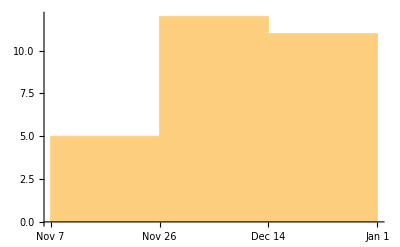

```mathematica
DateHistogram[%42]
```

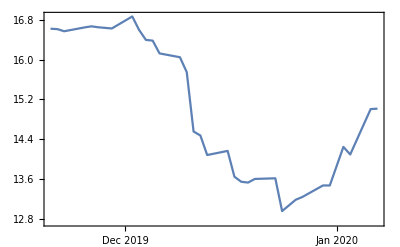

```mathematica
DateListPlot@Out[42]
```

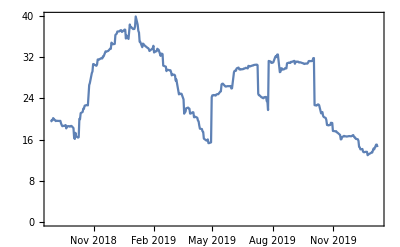

```mathematica
DateListPlot@FinancialData["NASDAQ:GOOG","Volatility50Day",DatePlus[-500]]
```

```mathematica
Entity["Financial","NASDAQ:GOOG"]
```

Alphabet Class C Shares

```mathematica
Entity["Financial","NASDAQ:GOOG"]["Dataset"]
```

Dataset[<>]

```mathematica
DeleteMissing@Entity["Financial","NASDAQ:GOOG"]["Dataset"]
```

Dataset[<>]

```mathematica
appl=FinancialData["NASDAQ:AAPL","Close",All]
```

TimeSeries[…]

```mathematica
applvol=FinancialData["NASDAQ:AAPL","Volume",All]
```

TemporalData[TimeSeries, <<1>>]

```mathematica
Join[
Transpose[{
appl["Dates"][[;;-2]],
Map[#-1&,Ratios@appl["Values"]]
}],
Transpose[{
applvol["Dates"],
applvol["Values"]
}]
]
```

{{Fri 12 Dec 1980 00:00:00GMT-8.,-0.0521738},{Mon 15 Dec 1980 00:00:00GMT-8.,-0.0733929},{Tue 16 Dec 1980 00:00:00GMT-8.,0.0247439},{Wed 17 Dec 1980 00:00:00GMT-8.,0.0290008},{Thu 18 Dec 1980 00:00:00GMT-8.,0.0610234},{Fri 19 Dec 1980 00:00:00GMT-8.,0.0486787},{Mon 22 Dec 1980 00:00:00GMT-8.,0.0421793},{Tue 23 Dec 1980 00:00:00GMT-8.,0.0526261},19702,{Mon 30 Dec 2019 00:00:00GMT-8.,36059614 shares},{Tue 31 Dec 2019 00:00:00GMT-8.,25247625 shares},{Thu 2 Jan 2020 00:00:00GMT-8.,33911864 shares},{Fri 3 Jan 2020 00:00:00GMT-8.,36633878 shares},{Mon 6 Jan 2020 00:00:00GMT-8.,29644644 shares},{Tue 7 Jan 2020 00:00:00GMT-8.,27877655 shares},{Wed 8 Jan 2020 00:00:00GMT-8.,32656885 shares}}
 |  |  |  |

```mathematica
Select[GatherBy[Out[51],First],Length@#==2&]
```

{{{Fri 12 Dec 1980 00:00:00GMT-8.,-0.0521738},{Fri 12 Dec 1980 00:00:00GMT-8.,117258400 shares}},{{Mon 15 Dec 1980 00:00:00GMT-8.,-0.0733929},{Mon 15 Dec 1980 00:00:00GMT-8.,43971200 shares}},{{Tue 16 Dec 1980 00:00:00GMT-8.,0.0247439},{Tue 16 Dec 1980 00:00:00GMT-8.,26432000 shares}},{{Wed 17 Dec 1980 00:00:00GMT-8.,0.0290008},{Wed 17 Dec 1980 00:00:00GMT-8.,21610400 shares}},9851,{{Fri 3 Jan 2020 00:00:00GMT-8.,0.00796825},{Fri 3 Jan 2020 00:00:00GMT-8.,36633878 shares}},{{Mon 6 Jan 2020 00:00:00GMT-8.,-0.00470305},{Mon 6 Jan 2020 00:00:00GMT-8.,29644644 shares}},{{Tue 7 Jan 2020 00:00:00GMT-8.,0.0160863},{Tue 7 Jan 2020 00:00:00GMT-8.,27877655 shares}}}
 |  |  |  |

```mathematica
Table[{First@First@s,Abs[(Last@First@s)/(QuantityMagnitude@Last@Last@s)]},{s,Out[52]}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{{Fri 12 Dec 1980 00:00:00GMT-8.,4.44947×10^-10},{Mon 15 Dec 1980 00:00:00GMT-8.,1.66911×10^-9},{Tue 16 Dec 1980 00:00:00GMT-8.,9.36133×10^-10},{Wed 17 Dec 1980 00:00:00GMT-8.,1.34198×10^-9},{Thu 18 Dec 1980 00:00:00GMT-8.,3.32328×10^-9},{Fri 19 Dec 1980 00:00:00GMT-8.,4.00397×10^-9},9846,{Mon 30 Dec 2019 00:00:00GMT-8.,2.02624×10^-10},{Tue 31 Dec 2019 00:00:00GMT-8.,9.03702×10^-10},{Thu 2 Jan 2020 00:00:00GMT-8.,2.86685×10^-10},{Fri 3 Jan 2020 00:00:00GMT-8.,2.1751×10^-10},{Mon 6 Jan 2020 00:00:00GMT-8.,1.58647×10^-10},{Tue 7 Jan 2020 00:00:00GMT-8.,5.77032×10^-10}}
 |  |  |  |

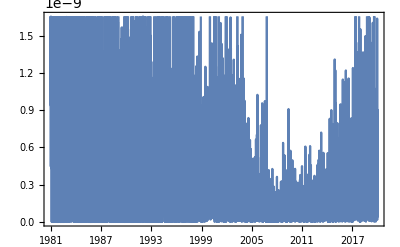

```mathematica
DateListPlot@Out[53]
```

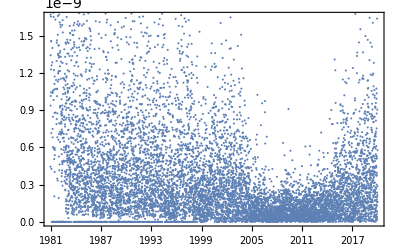

```mathematica
DateListPlot[Out[53],Joined->False]
```

```mathematica
DateListPlot[Out[53],Joined->False,PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
DateListPlot[Out[53],Joined->False,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
Out[100]
```

%100

```mathematica
Head@Out[100]
```

Out

```mathematica
SyntaxInformation[Out]
```

{ArgumentsPattern→{_.}}

```mathematica
"ArgumentsPattern"/.{"ArgumentsPattern"->{_.}}
```

{_.}

```mathematica
Standardize@{1,2,3}
```

{-1,0,1}

```mathematica
Standardize@{1,2,3,4,5,6}
```

{-5/(√14),-3/(√14),-1/(√14),1/(√14),3/(√14),5/(√14)}

```mathematica
Mean[{-5/(√14),-3/(√14),-1/(√14),1/(√14),3/(√14),5/(√14)}]
```

0

```mathematica
Total[{-5/(√14),-3/(√14),-1/(√14),1/(√14),3/(√14),5/(√14)}]
```

0

```mathematica
Normalize@{1,2,3,4,5,6}
```

{1/(√91),2/(√91),3/(√91),4/(√91),5/(√91),6/(√91)}

```mathematica
Norm[{1/(√91),2/(√91),3/(√91),4/(√91),5/(√91),6/(√91)}]
```

1

```mathematica
List@@Range@10
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range@3
```

{1,2,3}

```mathematica
Subsets[{1,2,3}]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Subsets[Range@4]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
Subsets[Range@5]
```

{{},{1},{2},{3},{4},{5},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5},{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5},{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5},{1,2,3,4,5}}

```mathematica
Histogram[
Map[Variance,Subsets[Range@5]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

Variance::shlen: The argument {} should have at least two elements.

Variance::shlen: The argument {1} should have at least two elements.

Variance::shlen: The argument {2} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

-Graphics-

```mathematica
Histogram[
Map[Variance,Subsets[Range@6]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

Variance::shlen: The argument {} should have at least two elements.

Variance::shlen: The argument {1} should have at least two elements.

Variance::shlen: The argument {2} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

-Graphics-

```mathematica
Histogram[
Map[Variance,Subsets[Range@7]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

Variance::shlen: The argument {} should have at least two elements.

Variance::shlen: The argument {1} should have at least two elements.

Variance::shlen: The argument {2} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

-Graphics-

```mathematica
Histogram[
Map[Variance,Subsets[Range@8]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

Variance::shlen: The argument {} should have at least two elements.

Variance::shlen: The argument {1} should have at least two elements.

Variance::shlen: The argument {2} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

-Graphics-

```mathematica
Histogram[
Map[Variance,Subsets[Range@10]],
PlotRange->Full,PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full,ColorFunction->"DarkRainbow"
]
```

Variance::shlen: The argument {} should have at least two elements.

Variance::shlen: The argument {1} should have at least two elements.

Variance::shlen: The argument {2} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

-Graphics-

```mathematica
DiscreteWaveletTransform[Map[Variance,Subsets[Range@10]]]
```

Variance::shlen: The argument {} should have at least two elements.

Variance::shlen: The argument {1} should have at least two elements.

Variance::shlen: The argument {2} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

DiscreteWaveletData[<<DWT>>, <10>, {1024}]

```mathematica
WaveletScalogram[%80]
```

Variance::shlen: The argument {1.} should have at least two elements.

Variance::shlen: The argument {2.} should have at least two elements.

Variance::shlen: The argument {3.} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

-Graphics-

```mathematica
WaveletMatrixPlot[%80]
```

WaveletMatrixPlot::rank: DiscreteWaveletData was computed using data of rank 1; data of rank 2 is expected.

WaveletMatrixPlot[DiscreteWaveletData[<<DWT>>, <10>, {1024}]]

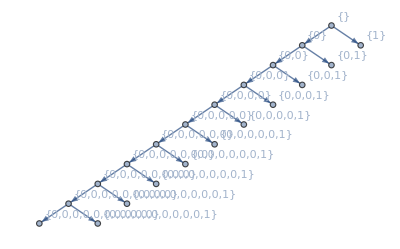

```mathematica
%80["TreeView"]
```

```mathematica
WaveletScalogram[DiscreteWaveletTransform[FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]
```

DiscreteWaveletTransform::wlist: Argument StructuredArray[QuantityArray,{9859},StructuredArray`StructuredData[QuantityArray,{0.5134,0.486614,0.4509,0.462057,0.475457,0.504471,0.529028,0.551342,0.580357,0.633928,0.642857,0.627242,0.609385,0.616071,0.602685,0.5759,0.551342,0.540185,«9823»,271.46,275.15,279.86,280.41,279.74,280.02,279.44,284.,284.27,289.91,289.8,291.52,293.65,300.35,297.43,299.8,298.39,303.19},USDollars,{{1}}]] should be one of rectangular array of any depth, image, sound, or sampled sound list.

WaveletScalogram::wd: First argument DiscreteWaveletTransform[StructuredArray[QuantityArray,{9859},StructuredArray`StructuredData[QuantityArray,{0.5134,0.486614,0.4509,0.462057,0.475457,0.504471,0.529028,0.551342,0.580357,0.633928,0.642857,0.627242,0.609385,0.616071,0.602685,0.5759,0.551342,0.540185,«9824»,275.15,279.86,280.41,279.74,280.02,279.44,284.,284.27,289.91,289.8,291.52,293.65,300.35,297.43,299.8,298.39,303.19},USDollars,{{1}}]]] to WaveletScalogram should be a DiscreteWaveletData or ContinuousWaveletData object.

WaveletScalogram[DiscreteWaveletTransform[QuantityArray[…]]]

```mathematica
DiscreteWaveletTransform[{56,40,8,24,48,48,40,16}]
```

DiscreteWaveletData[<<DWT>>, <3>, {8}]

```mathematica
WaveletScalogram[%85]
```

-Graphics-

```mathematica
data=Table[Sin[x^2],{x,0,10,0.02}];
```

```mathematica
dwd1=DiscreteWaveletTransform[data,DaubechiesWavelet[4],3];
dwd2=DiscreteWaveletTransform[data,SymletWavelet[4],3];
```

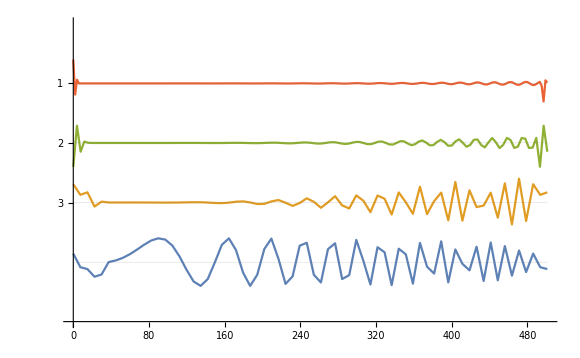
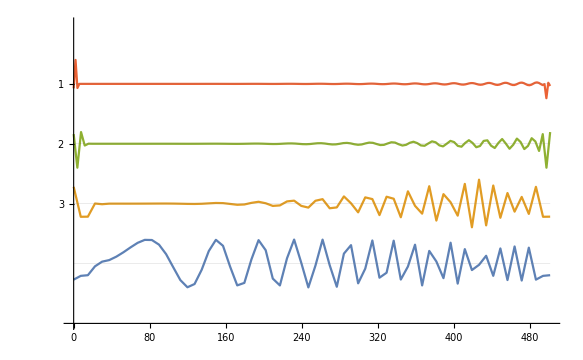

```mathematica
{WaveletListPlot[dwd1],WaveletListPlot[dwd2]}
```

```mathematica
data = Table[Sin[t^2],{t,-3π,3π,0.01}];
```

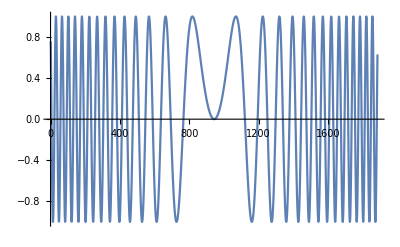

```mathematica
ListLinePlot[data]
```

```mathematica
dwd=DiscreteWaveletTransform[data,HaarWavelet[],3];
```

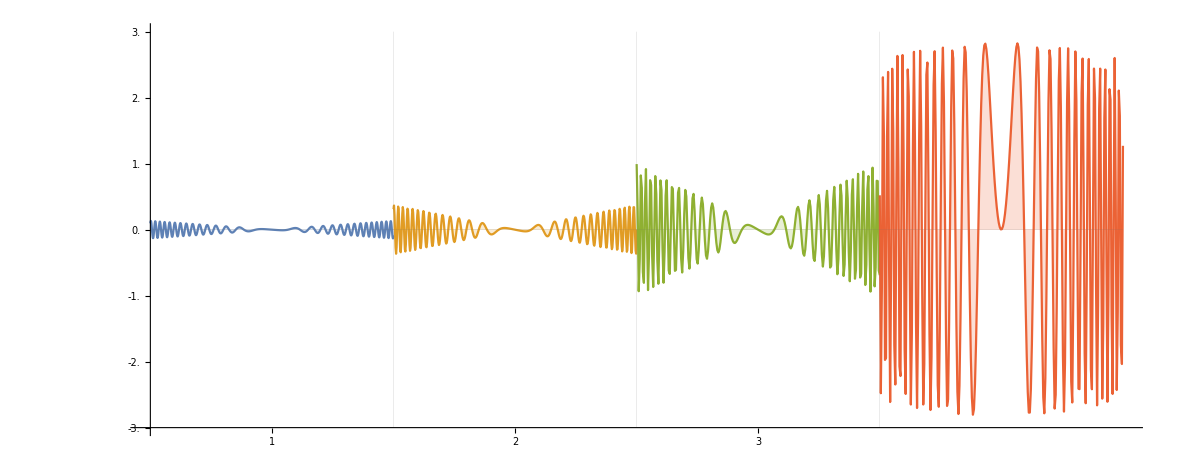

```mathematica
WaveletListPlot[dwd,PlotLayout->"CommonYAxis",Filling->Axis]
```